## Prepare

```mathematica
imgsize=600;
```

## Independent Random Variables

f(x) is a Gaussian distribution

```mathematica
f[x_]=Exp[-x^2/1]/(√2 Pi)
```

(ⅇ^(-x^2))/(√2 π)

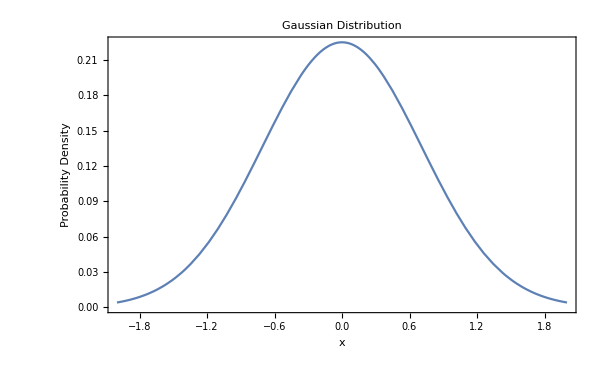

```mathematica
Plot[f[x],{x,-2,2},Frame->True,ImageSize->imgsize,PlotLabel->"Gaussian Distribution",FrameLabel->{"x","Probability Density"}]
```

g(x) is a uniform distribution

```mathematica
g[x_]:=Piecewise[{{1,-1<x<1},{0,x>=1||x≤-1}}]
```

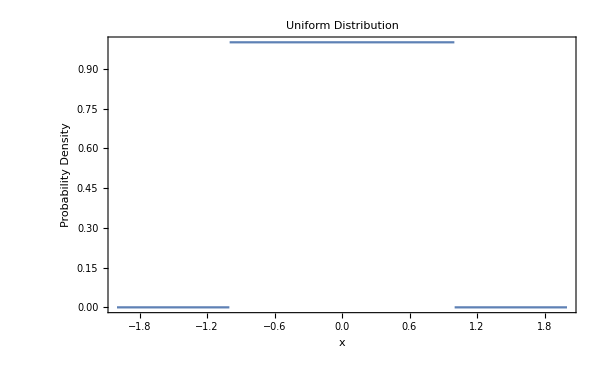

```mathematica
Plot[g[x],{x,-2,2},Frame->True,PlotLabel->"Uniform Distribution",FrameLabel->{"x","Probability Density"},ImageSize->imgsize]
```

Now define the probability density of the two inependent variables
h(x,y)=f(x) g(y)

```mathematica
h[x_,y_]:=f[x]*g[y]
```

```mathematica
Plot3D[h[x,y],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","P"},ImageSize->imgsize,PlotLabel->"Distribution of Two Independent Variables"]
```

-Graphics3D-